```mathematica
ResourceFunction["MultiwaySystem"][SubstitutionSystem[{"A"->"AA","B"->"AB"},"ABA",3]]
```

[{ABA,AAABAA,AAAAAAABAAAA,AAAAAAAAAAAAAAABAAAAAAAA}]

```mathematica
ResourceFunction["MultiwaySystem"][{"A"->"AA","B"->"AB"},"ABA",3,"StatesGraph"]
```

-Graphics-

```mathematica
SubstitutionSystem[{"A"->"AA","B"->"AB"},"ABA",3]
```

{ABA,AAABAA,AAAAAAABAAAA,AAAAAAAAAAAAAAABAAAAAAAA}

```mathematica
ResourceFunction["MultiwaySystem"][<|"A"->"AA","B"->"AB"|>,"ABA",3,"StatesGraph"]
```

[<|A→AA,B→AB|>,ABA,3,StatesGraph]

```mathematica
CellularAutomaton[30,{0,0,0,1,0,0,0},2]
```

{{0,0,0,1,0,0,0},{0,0,1,1,1,0,0},{0,1,1,0,0,1,0}}

```mathematica
ResourceFunction["MultiwaySystem"][CellularAutomaton[30,{0,0,0,1,0,0,0},2]]
```

[{{0,0,0,1,0,0,0},{0,0,1,1,1,0,0},{0,1,1,0,0,1,0}}]

```mathematica
Table[ResourceFunction["MultiwaySystem"][{"A"->"AA","B"->"AB"},"ABA",t,If[t<=5,"BranchialGraph","BranchialGraphStructure"]],{t,2,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TwoWayMultiReplace=ResourceFunction["https://www.wolframcloud.com/obj/wolframphysics/TwoWayMultiReplace"];
```

```mathematica
Column@Values@TwoWayMultiReplace[f[a_]<->f[f[a_],f[b_]],f[a_]<->f[f[a_],f[b_]],Method->"Bisubstitution","Uniquify"->True,"Canonicalize"->True]
```

f[f[f[a_],f[b_]]]<->f[f[f[a_]],f[c_]]
f[f[a_],f[b_]]<->f[f[a_],f[c_]]
f[f[a_]]<->f[f[f[f[a_],f[b_]]],f[c_]]
f[a_]<->f[f[f[a_],f[b_]],f[c_]]
f[a_]<->f[f[a_],f[f[f[b_],f[c_]]]]
f[a_]<->f[f[a_],f[f[b_],f[c_]]]
f[f[a_]]<->f[f[f[f[a_],f[b_]]],f[c_]]
f[f[f[a_],f[b_]]]<->f[f[f[a_]],f[c_]]
f[a_]<->f[f[a_],f[f[b_]]]
f[a_]<->f[a_]

```mathematica
Column@Values@TwoWayMultiReplace[f[a_]<->f[f[a_],f[b_]],f[a_]<->f[f[a_],f[b_]],Method->"Substitution","Uniquify"->True,"Canonicalize"->True]
```

f[f[a_],f[b_]]<->f[f[a_],f[c_]]
f[a_]<->f[f[f[a_],f[b_]],f[c_]]
f[a_]<->f[f[a_],f[f[b_],f[c_]]]
f[a_]<->f[a_]

```mathematica
axioms=ResourceFunction["https://www.wolframcloud.com/obj/wolframphysics/AxiomaticTheoryTWP"]["GroupAxioms"]
```

{a_∘(b_∘c_)<->(a_∘b_)∘c_,a_∘1<->a_,a_∘OverBar[a_]<->1}

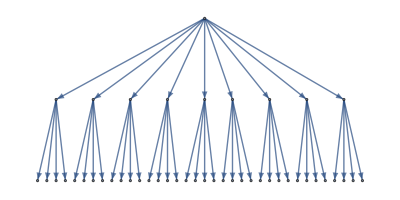

```mathematica
NestGraph[{state}|->Map[{tuple}|->Union@Join[Values@TwoWayMultiReplace[Sequence@@tuple,Method->"Bisubstitution","Uniquify"->True,"Canonicalize"->True],DeleteElements[state,tuple]],Tuples[state,{2}]],{axioms},2(*,VertexLabels->state_:->Column[state]*),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
```

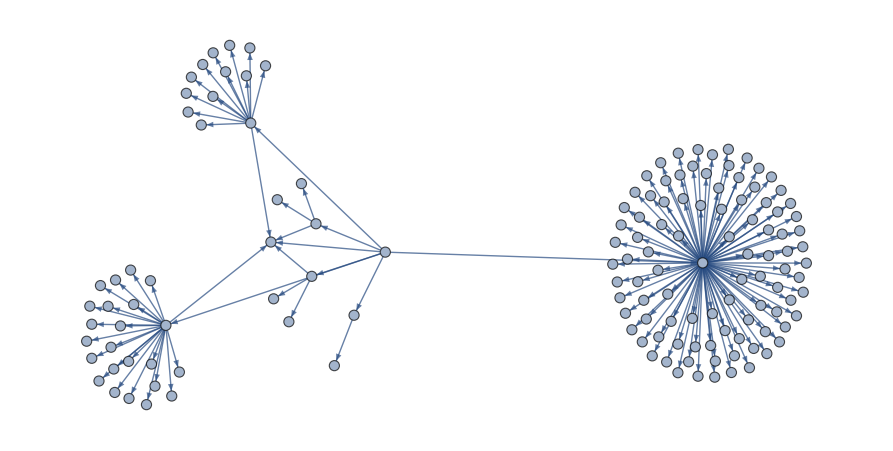

```mathematica
NestGraph[{state}|->Map[{tuple}|->Union@Join[Values@TwoWayMultiReplace[Sequence@@tuple]],Tuples[state,{2}]],{axioms},2,AspectRatio->1/2]
```

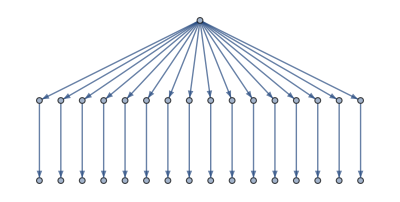

```mathematica
NestGraph[{state}|->Map[{tuple}|->Union@Join[Values@TwoWayMultiReplace[Sequence@@tuple]],Tuples[state,{2}]],{{{0,0,s___}:>{s,#a1,#a2,#a3},
{1,0,s___}:>{s,#b1,#b2},
{0,1,s___}:>{s,#c1,#c2,#c3},
{1,1,s___}:>{s,#d1,#d2}}},2,AspectRatio->1/2]
```

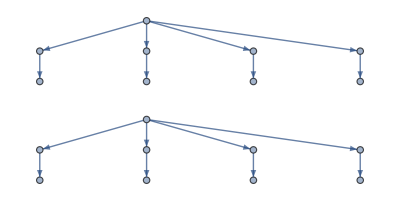

```mathematica
NestGraph[{state}|->Map[{tuple}|->Union@Join[Values@TwoWayMultiReplace[Sequence@@tuple]],Tuples[state,{2}]],{{0,_,_,s___}<->{s,0,0},{1,_,_,s___}<->Table[Prepend[RandomInteger[{0,1},4],s],10][[10]]},2,AspectRatio->1/2]
```

```mathematica
ResourceFunction["MultiwayTuringMachine"][{30},{{1,1,0},{0,1,0,0}},3,"StatesGraph",VertexSize->1]
```

-Graphics-

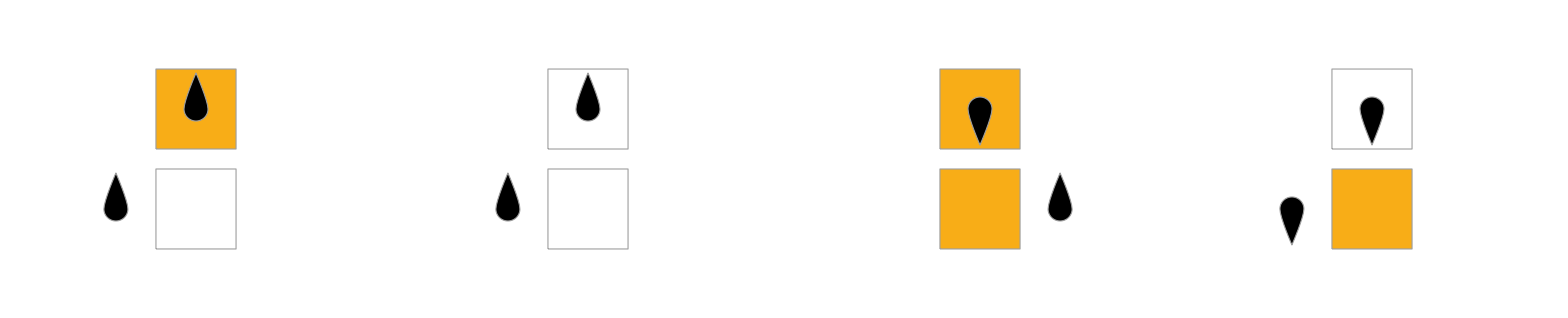

```mathematica
RulePlot[TuringMachine[30]]
```

```mathematica
RulePlot[TuringMachine["0"->"00","1"->"1101"],{1,{{},0}},20]
```

TuringMachine::init: The initial condition 1→1101 must take the form {statespec, tapespec}.

RulePlot[TuringMachine[0→00,1→1101],{1,{{},0}},20]

```mathematica
LayeredGraphPlot[ResourceFunction["MultiwaySystem"][{"Xo"->"oX","oX"->"Xo"},"ooooooooXoooXoooooooo",10,"EvolutionGraphStructure"]]
```

```mathematica
LayeredGraphPlot[ResourceFunction["MultiwaySystem"][{"0"->"00","1"->"1101"},"101",2,"EvolutionGraphStructure",AspectRatio->1],VertexRenderingFunction->({Text[#2,#1,{0,0},{0,1}]}&)]
```

-Graphics-

```mathematica
NestGraph[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},7,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

-Graphics-